### Equation

```mathematica
ψ
```

ψ

```mathematica
ODE=Function[{r,l,S},D[ψ[r],{r,2}]+2/r D[ψ[r],{r,1}]-l(l+1)/r^2 ψ[r]==S[l]]
```

Function[{r,l,S},∂_{r,2} ψ[r]+(2 ∂_{r,1} ψ[r])/r-(l (l+1) ψ[r])/r^2==S[l]]

```mathematica
ODE[r,0,S]
```

(2 ψ'[r])/r+ψ''[r]==S[0]

### Source

```mathematica
Source=Function[{r,θ,z0}, 1/(r^2+z0^2-2z0 r Cos[θ])^2]
```

Function[{r,θ,z0},1/((r^2+z0^2-2 z0 r Cos[θ])^2)]

```mathematica
S3D=Function[{x,y,z,z0},1/((x^2+y^2+(z-z0)^2)^2)]
```

Function[{x,y,z,z0},1/((x^2+y^2+(z-z0)^2)^2)]

```mathematica
S3D[r Sin[θ]Cos[ϕ],r Sin[θ]Sin[ϕ],r Cos[θ],z0d]//FullSimplify
```

1/((r^2+z0d^2-2 r z0d Cos[θ])^2)

```mathematica
Source[r,θ,z0d]-S3D[r Sin[θ]Cos[ϕ],r Sin[θ]Sin[ϕ],r Cos[θ],z0d]//FullSimplify
```

0

```mathematica
Source[z0,1,z0]
```

1/((2 z0^2-2 z0^2 Cos[1])^2)

```mathematica
Source[z0,0.1,z0]
```

10016.7/z0^4

```mathematica
rho=Function[{a,b,θ},1/(a^2(1-b Cos[θ])^2)]
```

Function[{a,b,θ},1/(a^2 (1-b Cos[θ])^2)]

```mathematica
afunc=r^2+z0^2
```

r^2+z0^2

```mathematica
D[afunc, r]
```

2 r

```mathematica
bfunc=2z0 Abs[r]/afunc
```

(2 z0 Abs[r])/(r^2+z0^2)

```mathematica
bfuncNoAbs=2z0 r/afunc
```

(2 r z0)/(r^2+z0^2)

```mathematica
rho[afunc,bfunc,θ]//Simplify
```

1/((r^2+z0^2-2 z0 Abs[r] Cos[θ])^2)

```mathematica
rho[a,b,θ]
```

1/(a^2 (1-b Cos[θ])^2)

```mathematica
S0=2Pi Integrate[rho[a,b,θ]SphericalHarmonicY[0,0,θ,ϕ]Sin[θ],{θ,0,Pi},Assumptions->{a∈Reals,a∈Reals,θ∈Reals,r∈Reals,z0∈Reals}]//Normal
```

-(2 √π)/(a^2 (-1+b^2))

```mathematica
S1=2Pi Integrate[rho[a,b,θ]SphericalHarmonicY[1,0,θ,ϕ]Sin[θ],{θ,0,Pi},Assumptions->{a∈Reals,a∈Reals,θ∈Reals,r∈Reals,z0∈Reals}]//Normal//Simplify
```

-(2 √(3 π) (b+(-1+b^2) ArcTanh[b]))/(a^2 b^2 (-1+b^2))

```mathematica
?Integrate
```

```mathematica
θ
```

θ

```mathematica
SAnalyticmodes[l_]:=2Pi Integrate[rho[a,b,θ]SphericalHarmonicY[l,0,θ,ϕ]Sin[θ],{θ,0,Pi},Assumptions->{a∈Reals,b∈Reals,θ∈Reals,r∈Reals,z0∈Reals}]//Normal//Simplify
```

```mathematica
SAnalyticmodes[0]
```

-(2 √π)/(a^2 (-1+b^2))

#### Examine S0

```mathematica
afunc
```

r^2+z0^2

```mathematica
S[0]=SAnalyticmodes[0]/.{a->afunc,b->bfunc}
```

-(2 √π)/((r^2+z0^2)^2 (-1+(4 z0^2 Abs[r]^2)/((r^2+z0^2)^2)))

```mathematica
SNoAbs[0]=(SAnalyticmodes[0]/.{a->afunc,b->bfuncNoAbs}//TrigToExp//Simplify)//PowerExpand
```

(2 √π)/((r^2-z0^2)^2)

#### Examine S1

```mathematica
SAnalyticmodes[1]
```

-(2 √(3 π) (b+(-1+b^2) ArcTanh[b]))/(a^2 b^2 (-1+b^2))

```mathematica
S[1]=SAnalyticmodes[1]/.{a->afunc,b->bfunc}
```

-(√(3 π) ((2 z0 Abs[r])/(r^2+z0^2)+(-1+(4 z0^2 Abs[r]^2)/((r^2+z0^2)^2)) ArcTanh[(2 z0 Abs[r])/(r^2+z0^2)]))/(2 z0^2 Abs[r]^2 (-1+(4 z0^2 Abs[r]^2)/((r^2+z0^2)^2)))

```mathematica
SNoAbs[1]=(SAnalyticmodes[1]/.{a->afunc,b->bfuncNoAbs})
```

-(√(3 π) ((2 r z0)/(r^2+z0^2)+(-1+(4 r^2 z0^2)/((r^2+z0^2)^2)) ArcTanh[(2 r z0)/(r^2+z0^2)]))/(2 r^2 z0^2 (-1+(4 r^2 z0^2)/((r^2+z0^2)^2)))

```mathematica
((SNoAbs[1]//TrigToExp)/. Log[arg_]:>Log[Together[arg]]//Simplify)//PowerExpand
```

1/(4 r^2 z0^2 (r^2-z0^2)^2)√(3 π) (4 r z0 (r^2+z0^2)+(r^2-z0^2)^2 (2 Log[r-z0]-Log[r^2+z0^2])-(r^2-z0^2)^2 (2 Log[r+z0]-Log[r^2+z0^2]))

#### Examine S2

```mathematica
S[2]=SAnalyticmodes[2]/.{a->afunc,b->bfunc}
```

(√(5 π) (r^2+z0^2) ((2 z0 Abs[r] (-3+(8 z0^2 Abs[r]^2)/((r^2+z0^2)^2)))/(r^2+z0^2)-3 (-1+(4 z0^2 Abs[r]^2)/((r^2+z0^2)^2)) ArcTanh[(2 z0 Abs[r])/(r^2+z0^2)]))/(4 z0^3 Abs[r]^3 (-1+(4 z0^2 Abs[r]^2)/((r^2+z0^2)^2)))

```mathematica
SNoAbs[2]=SAnalyticmodes[2]/.{a->afunc,b->bfuncNoAbs}//Simplify
```

(√(5 π) (6 r^5 z0-4 r^3 z0^3+6 r z0^5-3 (r^2-z0^2)^2 (r^2+z0^2) ArcTanh[(2 r z0)/(r^2+z0^2)]))/(4 r^3 z0^3 (r^2-z0^2)^2)

```mathematica
((SNoAbs[2]//TrigToExp)/. Log[arg_]:>Log[Together[arg]]//Simplify)//PowerExpand
```

(√(5 π) (6 r^5 z0-4 r^3 z0^3+6 r z0^5+3/2 (r^2-z0^2)^2 (r^2+z0^2) (2 Log[r-z0]-2 Log[r+z0])))/(4 r^3 z0^3 (r^2-z0^2)^2)

#### Examine S[>2]

```mathematica
SNoAbs[3]=SAnalyticmodes[3]/.{a->afunc,b->bfuncNoAbs}//Simplify
```

1/(16 r^4 z0^4 (r^2-z0^2)^2)√(7 π) (30 r^7 z0-14 r^5 z0^3-14 r^3 z0^5+30 r z0^7-3 (r^2-z0^2)^2 (5 r^4+6 r^2 z0^2+5 z0^4) ArcTanh[(2 r z0)/(r^2+z0^2)])

```mathematica
((SNoAbs[3]//TrigToExp)/. Log[arg_]:>Log[Together[arg]]//Simplify)//PowerExpand
```

1/(16 r^4 z0^4 (r^2-z0^2)^2)√(7 π) (30 r^7 z0-14 r^5 z0^3-14 r^3 z0^5+30 r z0^7+3/2 (r^2-z0^2)^2 (5 r^4+6 r^2 z0^2+5 z0^4) (2 Log[r-z0]-2 Log[r+z0]))

```mathematica
SNoAbs[3]//TrigToExp
```

1/(16 r^4 z0^4 (r^2-z0^2)^2)√(7 π) (30 r^7 z0-14 r^5 z0^3-14 r^3 z0^5+30 r z0^7-3/2 (r^2-z0^2)^2 (5 r^4+6 r^2 z0^2+5 z0^4) (-Log[1-(2 r z0)/(r^2+z0^2)]+Log[1+(2 r z0)/(r^2+z0^2)]))

Need to check Log[-(5+r)^2/(25+r^2)] , checked

```mathematica
SNoAbs[4]=SAnalyticmodes[4]/.{a->afunc,b->bfuncNoAbs}//Simplify
```

-1/(32 r^5 z0^5 (r^2-z0^2)^2)√π (-210 r^9 z0+80 r^7 z0^3+68 r^5 z0^5+80 r^3 z0^7-210 r z0^9+15 (r^2-z0^2)^2 (7 r^6+9 r^4 z0^2+9 r^2 z0^4+7 z0^6) ArcTanh[(2 r z0)/(r^2+z0^2)])

```mathematica
((SNoAbs[4]//TrigToExp)/. Log[arg_]:>Log[Together[arg]]//Simplify)//PowerExpand
```

-1/(32 r^5 z0^5 (r^2-z0^2)^2)√π (-210 r^9 z0+80 r^7 z0^3+68 r^5 z0^5+80 r^3 z0^7-210 r z0^9-15/2 (r^2-z0^2)^2 (7 r^6+9 r^4 z0^2+9 r^2 z0^4+7 z0^6) (2 Log[r-z0]-2 Log[r+z0]))

```mathematica
SNoAbs[5]=SAnalyticmodes[5]/.{a->afunc,b->bfuncNoAbs}//Simplify
```

-1/(256 r^6 z0^6 (r^2-z0^2)^2)√(11 π) (-630 r^11 z0+210 r^9 z0^3+164 r^7 z0^5+164 r^5 z0^7+210 r^3 z0^9-630 r z0^11+15 (r^2-z0^2)^2 (21 r^8+28 r^6 z0^2+30 r^4 z0^4+28 r^2 z0^6+21 z0^8) ArcTanh[(2 r z0)/(r^2+z0^2)])

```mathematica
((SNoAbs[5]//TrigToExp)/. Log[arg_]:>Log[Together[arg]]//Simplify)//PowerExpand
```

-1/(256 r^6 z0^6 (r^2-z0^2)^2)√(11 π) (-630 r^11 z0+210 r^9 z0^3+164 r^7 z0^5+164 r^5 z0^7+210 r^3 z0^9-630 r z0^11-15/2 (r^2-z0^2)^2 (21 r^8+28 r^6 z0^2+30 r^4 z0^4+28 r^2 z0^6+21 z0^8) (2 Log[r-z0]-2 Log[r+z0]))

```mathematica
SNoAbs[6]=SAnalyticmodes[6]/.{a->afunc,b->bfuncNoAbs}//Simplify
```

-1/(2560 r^7 z0^7 (r^2-z0^2)^2)√(13 π) (2 r z0 (-3465 r^12+1050 r^10 z0^2+777 r^8 z0^4+716 r^6 z0^6+777 r^4 z0^8+1050 r^2 z0^10-3465 z0^12)+105 (r^2-z0^2)^2 (33 r^10+45 r^8 z0^2+50 r^6 z0^4+50 r^4 z0^6+45 r^2 z0^8+33 z0^10) ArcTanh[(2 r z0)/(r^2+z0^2)])

```mathematica
((SNoAbs[6]//TrigToExp)/. Log[arg_]:>Log[Together[arg]]//Simplify)//PowerExpand
```

-1/(2560 r^7 z0^7 (r^2-z0^2)^2)√(13 π) (2 r z0 (-3465 r^12+1050 r^10 z0^2+777 r^8 z0^4+716 r^6 z0^6+777 r^4 z0^8+1050 r^2 z0^10-3465 z0^12)-105/2 (r^2-z0^2)^2 (33 r^10+45 r^8 z0^2+50 r^6 z0^4+50 r^4 z0^6+45 r^2 z0^8+33 z0^10) (2 Log[r-z0]-2 Log[r+z0]))

```mathematica
SNoAbs[7]=SAnalyticmodes[7]/.{a->afunc,b->bfuncNoAbs}//Simplify
```

-1/(2048 r^8 z0^8 (r^2-z0^2)^2)√((3 π)/5) (-30030 r^15 z0+8470 r^13 z0^3+6034 r^11 z0^5+5286 r^9 z0^7+5286 r^7 z0^9+6034 r^5 z0^11+8470 r^3 z0^13-30030 r z0^15+35 (r^2-z0^2)^2 (429 r^12+594 r^10 z0^2+675 r^8 z0^4+700 r^6 z0^6+675 r^4 z0^8+594 r^2 z0^10+429 z0^12) ArcTanh[(2 r z0)/(r^2+z0^2)])

```mathematica
((SNoAbs[7]//TrigToExp)/. Log[arg_]:>Log[Together[arg]]//Simplify)//PowerExpand
```

-1/(2048 r^8 z0^8 (r^2-z0^2)^2)√((3 π)/5) (-30030 r^15 z0+8470 r^13 z0^3+6034 r^11 z0^5+5286 r^9 z0^7+5286 r^7 z0^9+6034 r^5 z0^11+8470 r^3 z0^13-30030 r z0^15-35/2 (r^2-z0^2)^2 (429 r^12+594 r^10 z0^2+675 r^8 z0^4+700 r^6 z0^6+675 r^4 z0^8+594 r^2 z0^10+429 z0^12) (2 Log[r-z0]-2 Log[r+z0]))

```mathematica
SNoAbs[8]=SAnalyticmodes[8]/.{a->afunc,b->bfuncNoAbs}//Simplify
```

-((√(17 π) (-450450 r^17 z0+120120 r^15 z0^3+83160 r^13 z0^5+70344 r^11 z0^7+66932 r^9 z0^9+70344 r^7 z0^11+83160 r^5 z0^13+120120 r^3 z0^15-450450 r z0^17+315 (r^2-z0^2)^2 (715 r^14+1001 r^12 z0^2+1155 r^10 z0^4+1225 r^8 z0^6+1225 r^6 z0^8+1155 r^4 z0^10+1001 r^2 z0^12+715 z0^14) ArcTanh[(2 r z0)/(r^2+z0^2)]))/(143360 r^9 z0^9 (r^2-z0^2)^2))

```mathematica
((SNoAbs[8]//TrigToExp)/. Log[arg_]:>Log[Together[arg]]//Simplify)//PowerExpand
```

-((√(17 π) (-450450 r^17 z0+120120 r^15 z0^3+83160 r^13 z0^5+70344 r^11 z0^7+66932 r^9 z0^9+70344 r^7 z0^11+83160 r^5 z0^13+120120 r^3 z0^15-450450 r z0^17-315/2 (r^2-z0^2)^2 (715 r^14+1001 r^12 z0^2+1155 r^10 z0^4+1225 r^8 z0^6+1225 r^6 z0^8+1155 r^4 z0^10+1001 r^2 z0^12+715 z0^14) (2 Log[r-z0]-2 Log[r+z0])))/(143360 r^9 z0^9 (r^2-z0^2)^2))

```mathematica
SNoAbs[9]=SAnalyticmodes[9]/.{a->afunc,b->bfuncNoAbs}//Simplify
```

-((√(19 π) (-1531530 r^19 z0+390390 r^17 z0^3+264264 r^15 z0^5+217800 r^13 z0^7+200324 r^11 z0^9+200324 r^9 z0^11+217800 r^7 z0^13+264264 r^5 z0^15+390390 r^3 z0^17-1531530 r z0^19+315 (r^2-z0^2)^2 (2431 r^16+3432 r^14 z0^2+4004 r^12 z0^4+4312 r^10 z0^6+4410 r^8 z0^8+4312 r^6 z0^10+4004 r^4 z0^12+3432 r^2 z0^14+2431 z0^16) ArcTanh[(2 r z0)/(r^2+z0^2)]))/(458752 r^10 z0^10 (r^2-z0^2)^2))

```mathematica
((SNoAbs[9]//TrigToExp)/. Log[arg_]:>Log[Together[arg]]//Simplify)//PowerExpand
```

-((√(19 π) (-1531530 r^19 z0+390390 r^17 z0^3+264264 r^15 z0^5+217800 r^13 z0^7+200324 r^11 z0^9+200324 r^9 z0^11+217800 r^7 z0^13+264264 r^5 z0^15+390390 r^3 z0^17-1531530 r z0^19-315/2 (r^2-z0^2)^2 (2431 r^16+3432 r^14 z0^2+4004 r^12 z0^4+4312 r^10 z0^6+4410 r^8 z0^8+4312 r^6 z0^10+4004 r^4 z0^12+3432 r^2 z0^14+2431 z0^16) (2 Log[r-z0]-2 Log[r+z0])))/(458752 r^10 z0^10 (r^2-z0^2)^2))

```mathematica
SNoAbs[10]=SAnalyticmodes[10]/.{a->afunc,b->bfuncNoAbs}//Simplify
```

-((√(π/21) (-29099070 r^21 z0+7147140 r^19 z0^3+4750746 r^17 z0^5+3836976 r^15 z0^7+3442340 r^13 z0^9+3328664 r^11 z0^11+3442340 r^9 z0^13+3836976 r^7 z0^15+4750746 r^5 z0^17+7147140 r^3 z0^19-29099070 r z0^21+3465 (r^2-z0^2)^2 (4199 r^18+5967 r^16 z0^2+7020 r^14 z0^4+7644 r^12 z0^6+7938 r^10 z0^8+7938 r^8 z0^10+7644 r^6 z0^12+7020 r^4 z0^14+5967 r^2 z0^16+4199 z0^18) ArcTanh[(2 r z0)/(r^2+z0^2)]))/(393216 r^11 z0^11 (r^2-z0^2)^2))

```mathematica
((SNoAbs[10]//TrigToExp)/. Log[arg_]:>Log[Together[arg]]//Simplify)//PowerExpand
```

-((√(π/21) (-29099070 r^21 z0+7147140 r^19 z0^3+4750746 r^17 z0^5+3836976 r^15 z0^7+3442340 r^13 z0^9+3328664 r^11 z0^11+3442340 r^9 z0^13+3836976 r^7 z0^15+4750746 r^5 z0^17+7147140 r^3 z0^19-29099070 r z0^21-3465/2 (r^2-z0^2)^2 (4199 r^18+5967 r^16 z0^2+7020 r^14 z0^4+7644 r^12 z0^6+7938 r^10 z0^8+7938 r^8 z0^10+7644 r^6 z0^12+7020 r^4 z0^14+5967 r^2 z0^16+4199 z0^18) (2 Log[r-z0]-2 Log[r+z0])))/(393216 r^11 z0^11 (r^2-z0^2)^2))

### Analytical solution

```mathematica
YcontA[a_]:=1/Cos[γ[a]]^1;
```

```mathematica
ψAnalytic=Function[{x,y,z,z0},1/(2(x^2+y^2+(z-z0)^2))]
```

Function[{x,y,z,z0},1/(2 (x^2+y^2+(z-z0)^2))]

```mathematica
D[ψAnalytic[x,y,z,z0],{x,2}]+D[ψAnalytic[x,y,z,z0],{y,2}]+D[ψAnalytic[x,y,z,z0],{z,2}]-S3D[x,y,z,z0]//Simplify
```

0

```mathematica
ψAnalytictheta=ψAnalytic[r Sin[θ]Cos[ϕ],r Sin[θ]Sin[ϕ],r Cos[θ],z0]//FullSimplify
```

1/(50+2 r^2-20 r Cos[θ])

```mathematica
ψ0=2Pi Integrate[ψAnalytictheta SphericalHarmonicY[0,0,θ,ϕ]Sin[θ],{θ,0,Pi},Assumptions->{a∈Reals,a∈Reals,θ∈Reals,r∈Reals,z0∈Reals}]//Normal
```

(√π Log[(5+r)^2/(-5+r)^2])/(20 r)

```mathematica
Sourcetest=D[ψ0,{r,2}]+2/r D[ψ0,{r,1}]-l(l+1)/r^2 ψ0/.l->0//Simplify
```

(2 √π)/((-25+r^2)^2)

```mathematica
Sourcetest-SNoAbs[0]//Simplify
```

0

```mathematica
ψ1=2Pi Integrate[ψAnalytictheta SphericalHarmonicY[1,0,θ,ϕ]Sin[θ],{θ,0,Pi},Assumptions->{a∈Reals,a∈Reals,θ∈Reals,r∈Reals,z0∈Reals}]//Normal//Simplify
```

(√(3 π) (-20 r+(25+r^2) Log[(5+r)^2/(-5+r)^2]))/(200 r^2)

```mathematica
ψAnalyticmodes[l_]:=2Pi Integrate[ψAnalytictheta SphericalHarmonicY[l,0,θ,ϕ]Sin[θ],{θ,0,Pi},Assumptions->{a∈Reals,b∈Reals,θ∈Reals,r∈Reals,z0∈Reals}]//Normal//Simplify
```

```mathematica
ψAnalyticmodes[0]
```

(√π Log[(5+r)^2/(-5+r)^2])/(20 r)

```mathematica
%-ψ0//Simplify
```

0

```mathematica
ψAnalyticmodes[1]
```

(√(3 π) (-20 r+(25+r^2) Log[(5+r)^2/(-5+r)^2]))/(200 r^2)

```mathematica
ψAnalyticmodes[2]
```

(π (-60 r (25+r^2)+(1875+50 r^2+3 r^4) Log[(5+r)^2/(-5+r)^2]))/(800 √(5 π) r^3)

```mathematica
ψAnalyticmodes[3]
```

(√(7 π) (3 (25+r^2)^3 ArcTanh[(10 r)/(25+r^2)]-10 r (1875+70 r^2+3 r^4+9 r (25+r^2) Log[(5+r)^2/(-5+r)^2])))/(12000 r^4)

```mathematica
ψAnalyticmodes[4]
```

1/(320000 r^5)√π (-20 r (25+r^2) (13125-50 r^2+21 r^4)+6 (2734375+62500 r^2+2250 r^4+100 r^6+7 r^8) ArcTanh[(10 r)/(25+r^2)])

```mathematica
ψAnalyticmodes[5]
```

1/(48000000 r^6)√(11 π) (-20 r (73828125+2625000 r^2+101750 r^4+4200 r^6+189 r^8)+6 (25+r^2) (24609375-437500 r^2+36250 r^4-700 r^6+63 r^8) ArcTanh[(10 r)/(25+r^2)])

```mathematica
ψAnalyticmodes[6]
```

1/(320000000 r^7)√(13 π) (-140 r (25+r^2) (12890625-62500 r^2+19750 r^4-100 r^6+33 r^8)+(56396484375+1230468750 r^2+41015625 r^4+1562500 r^6+65625 r^8+3150 r^10+231 r^12) Log[(5+r)^2/(-5+r)^2])

```mathematica
ψAnalyticmodes[7]
```

1/(4480000000 r^8)√((3 π)/5) (-20 r (733154296875+25566406250 r^2+961953125 r^4+37787500 r^6+1539125 r^8+65450 r^10+3003 r^12)+7 (25+r^2) (104736328125-1933593750 r^2+151171875 r^4-3312500 r^6+241875 r^8-4950 r^10+429 r^12) Log[(5+r)^2/(-5+r)^2])

```mathematica
ψAnalyticmodes[8]
```

1/(358400000000 r^9)√(17 π) (-20 r (25+r^2) (2199462890625-11730468750 r^2+3314609375 r^4-22122500 r^6+77 r^8 (68875-390 r^2+117 r^4))+7 (196380615234375+4189453125000 r^2+135351562500 r^4+4921875000 r^6+191406250 r^8+7875000 r^10+346500 r^12+17160 r^14+1287 r^16) Log[(5+r)^2/(-5+r)^2])

```mathematica
ψAnalyticmodes[9]
```

1/(32256000000000 r^10)√(19 π) (-20 r (23369293212890625+r^2 (806469726562500+29912695312500 r^2+1151648437500 r^4+45524593750 r^6+33 r^8 (55837500+91 r^2 (25500+1100 r^2+51 r^4))))+63 (25+r^2) (370941162109375-6982421875000 r^2+r^4 (530664062500-12203125000 r^2+832656250 r^4-19525000 r^6+143 r^8 (9500-200 r^2+17 r^4))) Log[(5+r)^2/(-5+r)^2])

```mathematica
ψAnalyticmodes[10]
```

1/(153600000000000 √(21 π) r^11)π (-220 r (25+r^2) (40365142822265625+r^2 (-226611328125000+60305273437500 r^2-451546875000 r^4+94923593750 r^6+39 r^8 (-18525000+7 r^2 (565500-3400 r^2+969 r^4))))+63 (4404926300048828125+92735290527343750 r^2+2945709228515625 r^4+r^6 (104736328125000+3947753906250 r^2+155039062500 r^4+6316406250 r^6+143 r^8 (1875000+84375 r^2+4250 r^4+323 r^6))) Log[(5+r)^2/(-5+r)^2])

#### Plots of the solution in the imaginary plane

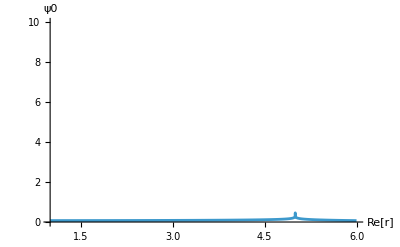

```mathematica
Plot[Abs[ψ0/.z0d->5/.r->x],{x,1,6},PlotRange->{0,10},AxesLabel->{"Re[r]","ψ0"}]
```

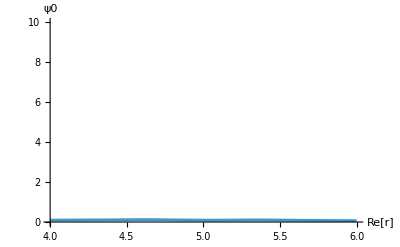

```mathematica
Plot[Abs[ψ0/.z0d->5/.r->γ[a]],{a,4,6},PlotRange->{0,10},AxesLabel->{"Re[r]","ψ0"}]
```

```mathematica
Plot3D[Abs[ψ0/.z0d->5/.r->x+I y],{x,4.5,5.5},{y,-3,3},PlotRange->{0,10},AxesLabel->{"Re[r]","Im[r]","ψ0"}]
```

-Graphics3D-

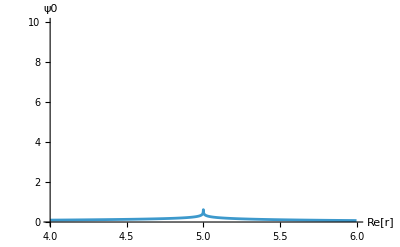

```mathematica
Plot[Abs[ψ1/.z0d->5/.r->x],{x,4,6},PlotRange->{0,10},AxesLabel->{"Re[r]","ψ0"}]
```

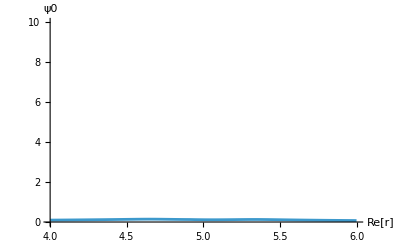

```mathematica
Plot[Abs[ψ1/.z0d->5/.r->γ[a]],{a,4,6},PlotRange->{0,10},AxesLabel->{"Re[r]","ψ0"}]
```

```mathematica
Plot3D[Abs[ψ1/.z0d->5/.r->x+I y],{x,4.5,5.5},{y,-3,3},PlotRange->{0,10},AxesLabel->{"Re[r]","Im[r]","ψ0"}]
```

-Graphics3D-